```mathematica
SetDirectory["/Users/guadalupecanasherrera/"];
```

```mathematica
Needs["PlotLegends`"];
```

Importación de los archivos   . dat

```mathematica
Tabla0=Import["datos_cosmo_0.dat"];
Tablaenergia=Import["datos_cosmo_0_energia.dat"];
Tablamateria=Import["datos_cosmo_0_Materia.dat"];
Tablaradiacion=Import["datos_cosmo_0_radiacion.dat"];
```

Gráficas
k=0

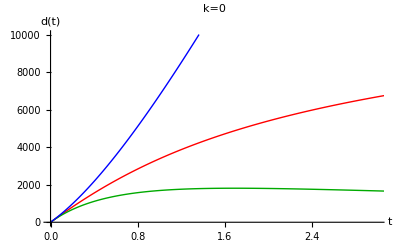

```mathematica
GraficasDistancias=ListPlot[{Tabla0[[1;;,{6,1}]], Tabla0[[1;;,{6,2}]],Tabla0[[1;;,{6,3}]]},PlotRange->{{0,3},{0.0,10000}},  Joined->True,AxesLabel->{t,"d(t)"}, LabelStyle->Directive[Black,Bold, 12], PlotLabel->Style[Framed["k=0"],12,Black,Background->LightGray], PlotLegend->{"d_propia", "d_angular", "d_luminosidad"}, LegendPosition->{1.1,-0.4}, PlotStyle-> {Directive[Red,Thick], Directive[Darker[Green],Thick],Directive[Blue,Thick]}]
```

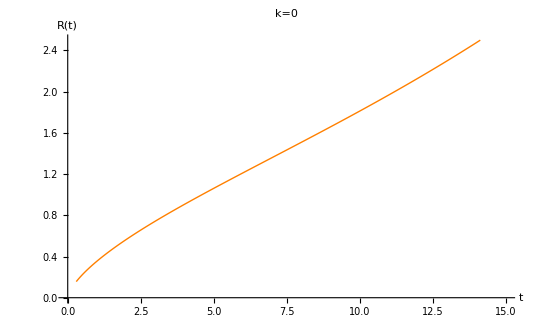

```mathematica
GraficasScaleFactor=ListPlot[{Tabla0[[1;;,{5,4}]]},PlotRange->{{0.0,15},{0.0,2.5}},  Joined->True,AxesLabel->{t,"R(t)"},LabelStyle->Directive[Black,Bold, 12], PlotLabel->Style[Framed["k=0"],12,Black,Background->LightGray], PlotStyle-> {Directive[Orange,Thick]}]
```

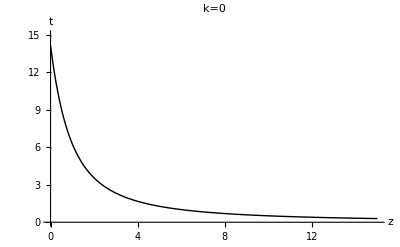

```mathematica
GraficasEdadZ=ListPlot[{Tabla0[[1;;,{6,5}]]},PlotRange->{{0.0,15},{0.0,15}},  Joined->True,AxesLabel->{z,"t"},LabelStyle->Directive[Black,Bold, 12], PlotLabel->Style[Framed["k=0"],12,Black,Background->LightGray], PlotStyle-> {Directive[Black,Thick]}]
```

k<0

```mathematica
GraficasDistancias=ListPlot[{TablaN[[1;;,{6,1}]], TablaN[[1;;,{6,2}]],TablaN[[1;;,{6,3}]]},PlotRange->{{0,15},{0.0,80000}},  Joined->True,AxesLabel->{t,"d(t)"}, LabelStyle->Directive[Black,Bold, 12], PlotLabel->Style[Framed["k=0"],12,Black,Background->LightGray], PlotLegend->{"d_propia", "d_angular", "d_luminosidad"}, LegendPosition->{1.1,-0.4}, PlotStyle-> {Directive[Red,Thick], Directive[Darker[Green],Thick],Directive[Blue,Thick]}];
```

```mathematica
GraficasScaleFactor=ListPlot[{TablaN[[1;;,{5,4}]]},PlotRange->{{0.0,15},{0.0,2.5}},  Joined->True,AxesLabel->{t,"R(t)"},LabelStyle->Directive[Black,Bold, 12], PlotLabel->Style[Framed["k=0"],12,Black,Background->LightGray], PlotStyle-> {Directive[Orange,Thick]}];
```

```mathematica
GraficasEdadZ=ListPlot[{TablaN[[1;;,{6,5}]]},PlotRange->{{0.0,15},{0.0,12}},  Joined->True,AxesLabel->{z,"t"},LabelStyle->Directive[Black,Bold, 12], PlotLabel->Style[Framed["k=0"],12,Black,Background->LightGray], PlotStyle-> {Directive[Black,Thick]}];
```

#### k>0

```mathematica
GraficasDistancias=ListPlot[{TablaP[[1;;,{6,1}]], TablaP[[1;;,{6,2}]],TablaP[[1;;,{6,3}]]},PlotRange->{{0,15},{0.0,80000}},  Joined->True,AxesLabel->{t,"d(t)"}, LabelStyle->Directive[Black,Bold, 12], PlotLabel->Style[Framed["k=0"],12,Black,Background->LightGray], PlotLegend->{"d_propia", "d_angular", "d_luminosidad"}, LegendPosition->{1.1,-0.4}, PlotStyle-> {Directive[Red,Thick], Directive[Darker[Green],Thick],Directive[Blue,Thick]}];
```

```mathematica
GraficasScaleFactor=ListPlot[{TablaP[[1;;,{5,4}]]},PlotRange->{{0.0,15},{0.0,2.5}},  Joined->True,AxesLabel->{t,"R(t)"},LabelStyle->Directive[Black,Bold, 12], PlotLabel->Style[Framed["k=0"],12,Black,Background->LightGray], PlotStyle-> {Directive[Orange,Thick]}];
```

```mathematica
GraficasEdadZ=ListPlot[{TablaP[[1;;,{6,5}]]},PlotRange->{{0.0,15},{0.0,12}},  Joined->True,AxesLabel->{z,"t"},LabelStyle->Directive[Black,Bold, 12], PlotLabel->Style[Framed["k=0"],12,Black,Background->LightGray], PlotStyle-> {Directive[Black,Thick]}];
```

## GRAFICA DE TODOS LOS R(T) PARA LAS DIFERENTES COMPOSICIONES

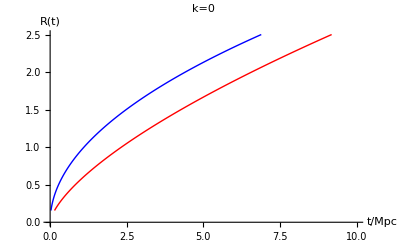

```mathematica
GraficasScaleFactorComposicion= ListPlot[{Tablamateria[[1;;,{5,4}]], Tablaradiacion[[1;;,{5,4}]]}, PlotRange->{{0.0,10},{0.0,2.5}},  Joined->True,AxesLabel->{"t/Mpc","R(t)"},LabelStyle->Directive[Black,Bold, 12], PlotLabel->Style[Framed["k=0"],12,Black,Background->LightGray],  PlotStyle-> {Directive[Red,Thick],Directive[Blue,Thick]},  PlotLegend->{"Materia", "Radiacion"}, LegendPosition->{1.1,-0.4}]
```

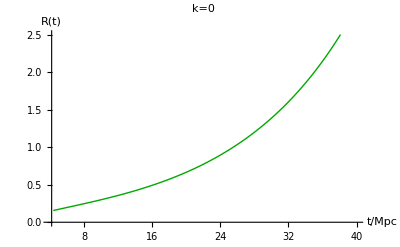

```mathematica
GraficasScaleFactorComposicion= ListPlot[{Tablaenergia[[1;;,{5,4}]]}, PlotRange->{{4.0,40},{0.0,2.5}},  Joined->True,AxesLabel->{"t/Mpc","R(t)"},LabelStyle->Directive[Black,Bold, 12], PlotLabel->Style[Framed["k=0"],12,Black,Background->LightGray],  PlotStyle-> {Directive[Darker[Green],Thick]},  PlotLegend->{"Energia Oscura"}, LegendPosition->{1.1,-0.4}]
```